# 化合物検索アルゴリズムの開発

## Program

```mathematica
home="/home/kamano/"
```

/home/kamano/

```mathematica
(*home="/Users/kouamano/"*)
```

```mathematica
SetDirectory[home<>"gitsrc/Chemical-form_search_by_Eigen"]
```

/home/kamano/gitsrc/Chemical-form_search_by_Eigen

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/List_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Chemicalform_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]
```

## 技術調査

## スペクトラルグラフ理論とは

グラフの隣接行列を特性方程式問題として扱う:

インプット = > 隣接行列
アウトプット = > 固有値・固有ベクトル
パラメーター => 
	- コネクション要素の値
	- トレースの値
	- ベースの値
	- 有向/無向

(a | B | B | X1
B | b | B | X2
B | B | c | X3
X1 | X2 | X3 | d) (e | X4 | B
X4 | f | X5
B | X5 | g)

B : ベース; X : コネクション(配置が対称なら無向); {a,b,c,d,e,f,g} : トレース。
Xの配置のみが決まっており、あとは編集可。



```mathematica
v={1,2,3,4};e={1<->2,1<->3,1<->4};gr=Graph[v,e]
```

```mathematica
(am=AdjacencyMatrix[gr])//MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

## 隣接行列とその固有値・固有ベクトル(を求めるアルゴリズム)の一般的な性質

固有値はノルムの大きい順に求まる

固有値の合計はコネクションの影響を受けない

固有ベクトルのノルムは1となる(Mathematicaではそうならない)

元の行列の行・列を同じオーダーで入れ替えても固有値は変化しない、ただし固有ベクトルの要素の順は変更される

対角行列では固有値は対角要素となり、固有ベクトルは直交する

コネクションの強度が強いほど、固有値への、固有ベクトルへの影響は大きい

```mathematica
(es=Eigensystem[am]);{es[[1]]//MatrixForm,es[[2]]//MatrixForm}//TableForm
```

(-√3
√3
0
0)
(-√3 | 1 | 1 | 1
√3 | 1 | 1 | 1
0 | -1 | 0 | 1
0 | -1 | 1 | 0)

```mathematica
Map[MatrixForm,Eigensystem[matReOrder[AdjacencyMatrix[gr]//Normal,{3,2,4,1}]]]//TableForm
```

(-√3
√3
0
0)
(-1/(√3) | -1/(√3) | -1/(√3) | 1
1/(√3) | 1/(√3) | 1/(√3) | 1
-1 | 0 | 1 | 0
-1 | 1 | 0 | 0)

```mathematica
ex1={{4,0,0,0},
{0,3,0,0},
{0,0,2,0},
{0,0,0,1}
}
```

{{4,0,0,0},{0,3,0,0},{0,0,2,0},{0,0,0,1}}

```mathematica
Map[MatrixForm,nex1=nEingensystem[ex1]]//TableForm
```

(4
3
2
1)
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
ex2={{4,0,0,0.1},
{0,3,0,0},
{0,0,2,0},
{0.1,0,0,1}
}
```

{{4,0,0,0.1},{0,3,0,0},{0,0,2,0},{0.1,0,0,1}}

```mathematica
Map[MatrixForm,nex2=nEingensystem[ex2]]//TableForm
```

(4.00333
3.
2.
0.99667)
(-0.999446 | 0. | 0. | -0.0332779
0. | 1. | 0. | 0.
0. | 0. | -1. | 0.
-0.0332779 | 0. | 0. | 0.999446)

```mathematica
Tr[nex2[[1]]]
```

10.

## スペクトラルグラフ理論を応用した化合物検索の先行事例

Milan Randic. 
On Characterization of Molecular Branching. 
Journal of The American Chemical Society. 
Vol.97, Num.23, p .6609. 
1975.

Frank R. Burden. 
Molecular Identification Number for Substructure Searches.
Journal of Chemical Information and Computer Sciences. 
Vol. 29, p.225. 
1989.

いずれも、系統の近い分子のマッチングに有効。

## アルゴリズム提案

本質的に、あらゆる系統の単独分子同士のマッチングに応用可能な方法を目指す。

## 技術コンセプト

固有値列 (パワースペクトル) のみを利用する(固有ベクトルの差は無視する )

対角要素に原子番号を付与することにより原子集合を構成・区別する

原子番号(構成原子の種類)とコネクションの強度を設定することによりうまく(目的別に)分子を区別できないか？

ひとまず2分子マッチを前提とする

双方の共通な原子集合を構成し、差異はコネクションを利用する

## アルゴリズム定義

### Pseudo Code

0   (***** Pseudo Code *****)
1   Compound A
2   Compound B
3
4   AC = AtomCount (A, B)
5
6   BM[A] = AddBond (AC, A, tr = "Atomic number", bond = "Order", bg = 0)
7   BM[B] = AddBond (AC, B, tr = "Atomic number", bond = "Order", bg = 0)
8 
9    EVL[A] = Normalize (Eigenvalues (BM[A]))
10 EVL[B] = Normalize (Eigenvalues (BM[B]))
11
12  { IDX[A, B] = Inner (EVL[A], EVL[B])
13  OR
14  IDX[A, B] = Dist (EVL[A], EVL[B]) }
15  (* Parameters: tr,bond, bg. *)

### Work Flow

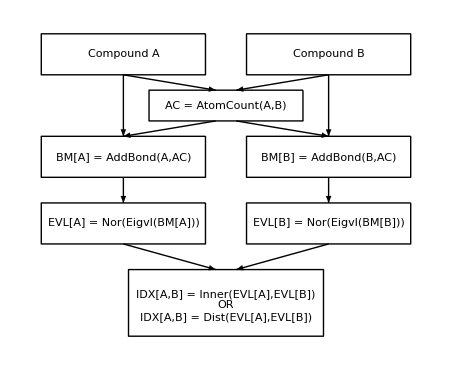

## 実装例(クラスタリング)

| 隣接行列 A | 隣接行列 B | ...
Parameter α | Classify[A,α] | Classify[B,α] | 
Parameter β | Classify[A,β] |  | 
... |  |  | 
 |      ↓ |  | 
 |  |  | 
 | 指標による選択 |  |

※クラスタリングの評価には次式を利用：

(SI = K (∏_(i=1)^K n[i]^(d[i]/D)))^(1/K)

K :  クラスタ数; 
n[i] : クラスタiのメンバー数; 
d[i] : クラスタiのdispersion (半径などの代表距離); 
D : 全サンプルにおけるdispersion (半径などの代表距離).
値が小さいほど適正

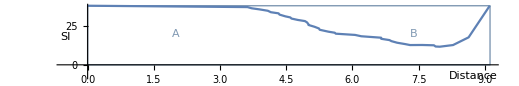
-Graphics-木の評価：A/(A + B)

## Clustering of Amino Acids

### Data

```mathematica
Get["local.data"];
```

```mathematica
AA
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
numAA
```

20

```mathematica
AAName
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
AAFig//Length
```

20

```mathematica
AAFig45
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AAAdjMat//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{«1»},«17»,{«1»}}

```mathematica
AAVT//Short
```

{{C,C,N,O,O,H,H,H,H,H},«18»,{C,C,C,C,C,C,N,«13»,C,H,H,H,O,O,H}}

```mathematica
elmAAAdjMat//Dimensions
```

{20}

```mathematica
AADmat//Dimensions
```

{20,20}

### Clustering

Candidate:

```mathematica
ag["A"]=DirectAgglomerate[AADmat,Linkage->"Average"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[1,Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],6,0.798298,3,1],1.31674,1,4],Cluster[Cluster[Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.5617,2,1],0.704903,1,3],Cluster[16,18,0.92273,1,1],1.56884,4,2],Cluster[Cluster[4,Cluster[Cluster[5,15,0.466146,1,1],Cluster[8,9,0.522399,1,1],0.835355,2,2],0.928711,1,4],13,1.04394,5,1],1.81684,6,6],2.22909,5,12],Cluster[20,Cluster[19,17,0.588454,1,1],1.63161,1,2],4.08975,17,3]

```mathematica
ag["WA"]=DirectAgglomerate[AADmat,Linkage->"WeightedAverage"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],0.994135,1,3],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.844398,2,1],0.927675,1,3],Cluster[Cluster[5,15,0.466146,1,1],6,0.819333,2,1],1.08802,4,3],1.58344,4,7],Cluster[Cluster[18,16,0.92273,1,1],Cluster[Cluster[11,Cluster[14,10,0.468095,1,1],0.5617,1,2],12,0.659033,3,1],1.65253,2,4],2.03674,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.63161,2,1],3.73837,17,3]

```mathematica
ag["W"]=DirectAgglomerate[AADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],4.67907,5,6],Cluster[Cluster[16,18,0.92273,1,1],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.592902,2,1],0.723301,1,3],3.19682,2,4],7.56004,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.97933,2,1],12.9788,17,3]

```mathematica
ag["C"]=DirectAgglomerate[AADmat,Linkage->"Centroid"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[1,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.596282,2,1],6,0.645681,3,1],Cluster[5,15,0.466146,1,1],0.646992,4,2],Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.713799,2,1],0.681986,1,3],0.729913,6,4],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.444676,2,1],0.482201,1,3],1.02204,10,4],Cluster[16,18,0.92273,1,1],1.27935,14,2],1.46387,1,16],Cluster[20,Cluster[19,17,0.588454,1,1],1.4845,1,2],2.54486,17,3]

### Selection

#### Method["A"]

```mathematica
meth="A"
```

A

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,7.20962,7.42148,7.63739,7.99359,8.70209,9.5186,10.3446,11.162,11.9413,12.776,13.6574,14.5075,15.4058,16.2942,17.2057,18.1269,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{4.08975,2.22909,1.81684,1.63161,1.56884,1.31674,1.04394,0.928711,0.92273,0.835355,0.798298,0.704903,0.669325,0.588454,0.5617,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{4.08975,20.},{2.22909,7.11861},{1.81684,7.20962},{1.63161,7.42148},{1.56884,7.63739},{1.31674,7.99359},{1.04394,8.70209},{0.928711,9.5186},{0.92273,10.3446},{0.835355,11.162},{0.798298,11.9413},{0.704903,12.776},{0.669325,13.6574},{0.588454,14.5075},{0.5617,15.4058},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.403983

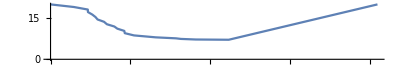

```mathematica
ListPlot[pt["A"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["WA"]

```mathematica
meth="WA"
```

WA

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,7.18004,6.96998,7.26336,7.97071,8.7945,9.53531,10.3385,11.1561,11.9611,12.776,13.6236,14.5075,15.4058,16.2942,17.2057,18.1269,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{3.73837,2.03674,1.65253,1.63161,1.58344,1.08802,0.994135,0.927675,0.92273,0.844398,0.819333,0.669325,0.659033,0.588454,0.5617,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{3.73837,20.},{2.03674,7.11861},{1.65253,7.18004},{1.63161,6.96998},{1.58344,7.26336},{1.08802,7.97071},{0.994135,8.7945},{0.927675,9.53531},{0.92273,10.3385},{0.844398,11.1561},{0.819333,11.9611},{0.669325,12.776},{0.659033,13.6236},{0.588454,14.5075},{0.5617,15.4058},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.397261

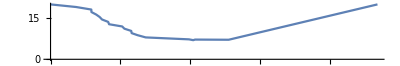

```mathematica
ListPlot[pt["WA"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["W"]

```mathematica
meth="W"
```

W

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,7.18004,7.42148,7.57266,7.99359,8.70209,9.51355,10.2962,11.1119,11.9181,12.7504,13.6322,14.5075,15.3948,16.2942,17.2057,18.1269,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{12.9788,7.56004,4.67907,3.19682,1.97933,1.43447,1.43198,1.05103,1.02298,0.951732,0.92273,0.723301,0.71254,0.592902,0.588454,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{12.9788,20.},{7.56004,7.11861},{4.67907,7.18004},{3.19682,7.42148},{1.97933,7.57266},{1.43447,7.99359},{1.43198,8.70209},{1.05103,9.51355},{1.02298,10.2962},{0.951732,11.1119},{0.92273,11.9181},{0.723301,12.7504},{0.71254,13.6322},{0.592902,14.5075},{0.588454,15.3948},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.491365

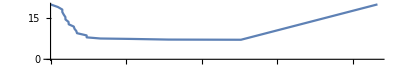

```mathematica
ListPlot[pt["W"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["C"]

```mathematica
meth="C"
```

C

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,6.21464,6.6581,7.27153,7.94482,8.71099,9.55628,10.3587,11.1548,11.9413,12.776,13.6236,14.5204,15.43,16.3164,17.2373,18.1272,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{2.54486,1.4845,1.46387,1.27935,1.02204,0.92273,0.729913,0.713799,0.681986,0.646992,0.645681,0.596282,0.588454,0.522399,0.482201,0.468095,0.466146,0.444676,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{2.54486,20.},{1.4845,7.11861},{1.46387,6.21464},{1.27935,6.6581},{1.02204,7.27153},{0.92273,7.94482},{0.729913,8.71099},{0.713799,9.55628},{0.681986,10.3587},{0.646992,11.1548},{0.645681,11.9413},{0.596282,12.776},{0.588454,13.6236},{0.522399,14.5204},{0.482201,15.43},{0.468095,16.3164},{0.466146,17.2373},{0.444676,18.1272},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.388078

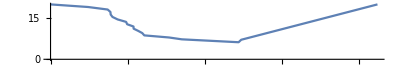

```mathematica
ListPlot[pt["C"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

### Plot

```mathematica
dAreaRatio[pt["A"]]
dAreaRatio[pt["WA"]]
dAreaRatio[pt["W"]]
dAreaRatio[pt["C"]]
```

0.403983

0.397261

0.491365

0.388078

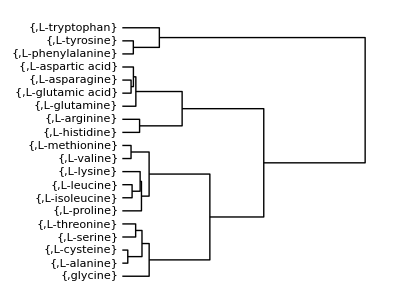

```mathematica
DendrogramPlot[ag["W"],LeafLabels->({AAFig45[[#]],AAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

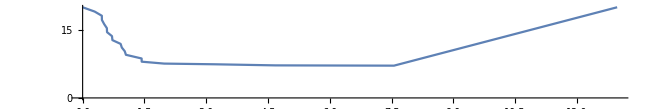

```mathematica
ListPlot[pt["W"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

## Clustering of Amino Acids + Lipids

### Data

Getting the information of lipids

```mathematica
lipidsNonIso
```

{heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

Merging

```mathematica
LPAA
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
numLPAA
```

38

```mathematica
LPAAName
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
LPAAFig//Length
```

38

```mathematica
LPAAFig45
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LPAAAdjMat
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,0},{0,1,0,0,0,0,0,1,0,0},{0,2,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,2,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,1,0},8,{0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0}},34,{1},{1}}
 |  |  |  |

```mathematica
LPAAVT
```

{{C,C,N,O,O,H,H,H,H,H},{O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,N,O,O,H,H,H,H,C,O,C,H,H,H,H,H},{S,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,O,O,H,H,H,H,H,H,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{S,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,C,N,N,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,O,C,C,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,N,C,C,C,H,C,H,H,H,H,H,H,H,N,C,H,H,H,O,O,H},{C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{K,O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{P,O,O,O,O,N,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H}}

```mathematica
elmLPAAAdjMat//Dimensions
```

{38}

```mathematica
LPAADmat//Dimensions
```

{38,38}

### Clustering

```mathematica
lpaaag["A"]=DirectAgglomerate[LPAADmat,Linkage->"Average"]
```

DirectAgglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],6,0.798298,3,1],1.31674,1,4],Cluster[Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.5617,2,1],12,0.704903,3,1],Cluster[16,18,0.92273,1,1],1.56884,4,2],2.54662,5,6],Cluster[Cluster[Cluster[Cluster[Cluster[4,Cluster[Cluster[5,15,0.466146,1,1],Cluster[8,9,0.522399,1,1],0.835355,2,2],0.928711,1,4],13,1.04394,5,1],22,1.33667,6,1],Cluster[24,Cluster[25,Cluster[26,27,0.,1,1],0.,1,2],0.954164,1,3],1.8004,7,4],21,2.13807,11,1],2.74846,11,12],Cluster[Cluster[Cluster[Cluster[Cluster[30,28,0.,1,1],29,0.581246,2,1],Cluster[Cluster[32,Cluster[33,36,0.,1,1],0.,1,2],Cluster[35,Cluster[34,31,0.,1,1],0.183172,1,2],0.827947,3,3],1.27911,3,6],37,1.65749,9,1],Cluster[Cluster[17,19,0.588454,1,1],Cluster[20,23,0.961533,1,1],1.54483,2,2],3.01638,10,4],3.61711,23,14],38,5.55312,37,1]

```mathematica
lpaaag["WA"]=DirectAgglomerate[LPAADmat,Linkage->"WeightedAverage"]
```

DirectAgglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],0.994135,1,3],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.844398,2,1],0.927675,1,3],Cluster[Cluster[5,15,0.466146,1,1],6,0.819333,2,1],1.08802,4,3],1.58344,4,7],Cluster[Cluster[18,16,0.92273,1,1],Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.5617,2,1],12,0.659033,3,1],1.65253,2,4],2.03674,11,6],Cluster[21,Cluster[24,22,1.00798,1,1],1.90489,1,2],2.34774,17,3],Cluster[Cluster[Cluster[Cluster[Cluster[33,Cluster[32,36,0.,1,1],0.,1,2],Cluster[Cluster[34,31,0.,1,1],35,0.183172,2,1],0.820546,3,3],Cluster[Cluster[Cluster[30,28,0.,1,1],29,0.581246,2,1],Cluster[25,Cluster[26,27,0.,1,1],0.,1,2],0.952993,3,3],1.60666,6,6],37,1.73514,12,1],Cluster[Cluster[23,20,0.961533,1,1],Cluster[17,19,0.588454,1,1],1.54483,2,2],2.83627,13,4],3.6417,20,17],38,5.64929,37,1]

```mathematica
lpaaag["W"]=DirectAgglomerate[LPAADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],Cluster[21,Cluster[22,24,1.00798,1,1],2.20387,1,2],3.62661,6,3],6.28158,5,9],Cluster[Cluster[16,18,0.92273,1,1],Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.592902,2,1],12,0.723301,3,1],3.19682,2,4],7.67005,14,6],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[34,31,0.,1,1],35,0.244229,2,1],Cluster[Cluster[30,28,0.,1,1],29,0.774995,2,1],2.23878,3,3],37,2.3346,6,1],Cluster[33,Cluster[32,36,0.,1,1],0.,1,2],3.68258,7,3],Cluster[27,Cluster[25,26,0.,1,1],0.,1,2],5.51745,10,3],Cluster[Cluster[Cluster[17,19,0.588454,1,1],Cluster[20,23,0.961533,1,1],2.31466,2,2],38,6.97161,4,1],10.7161,13,5],36.6737,20,18]

```mathematica
lpaaag["C"]=DirectAgglomerate[LPAADmat,Linkage->"Centroid"]
```

DirectAgglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.596282,2,1],6,0.645681,3,1],Cluster[5,15,0.466146,1,1],0.646992,4,2],Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.713799,2,1],0.681986,1,3],0.729913,6,4],Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.444676,2,1],12,0.482201,3,1],1.02204,10,4],22,1.2313,14,1],Cluster[18,16,0.92273,1,1],1.24598,15,2],1.48359,1,17],21,1.73955,18,1],Cluster[Cluster[Cluster[17,19,0.588454,1,1],Cluster[23,20,0.961533,1,1],1.15733,2,2],Cluster[37,Cluster[Cluster[Cluster[Cluster[Cluster[30,28,0.,1,1],29,0.581246,2,1],Cluster[Cluster[34,31,0.,1,1],35,0.183172,2,1],0.746259,3,3],Cluster[36,Cluster[32,33,0.,1,1],0.,1,2],0.936237,6,3],Cluster[Cluster[26,Cluster[27,25,0.,1,1],0.,1,2],24,0.954164,3,1],1.23731,9,4],1.19898,1,13],1.71673,4,14],1.92345,19,18],38,4.30864,37,1]

### Selection

#### Method["A"]

```mathematica
meth="A"
```

A

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,11.0542,10.6177,9.33586,10.9555,11.0021,11.5538,11.6689,12.3796,12.9409,13.5517,14.367,15.1798,15.9028,16.7848,17.6482,18.4522,19.3402,20.2172,21.0631,21.8101,22.6946,23.6106,24.503,25.4294,26.3276,27.2468,28.1823,29.1247,30.0674,31.0316,32.,33.,34.,35.,36.,37.,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{5.55312,3.61711,3.01638,2.74846,2.54662,2.13807,1.8004,1.65749,1.56884,1.54483,1.33667,1.31674,1.27911,1.04394,0.961533,0.954164,0.928711,0.92273,0.835355,0.827947,0.798298,0.704903,0.669325,0.588454,0.581246,0.5617,0.522399,0.468095,0.466146,0.292172,0.183172,0.,0.,0.,0.,0.,0.,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,37,37,37,37,37,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{5.55312,38.},{3.61711,11.0542},{3.01638,10.6177},{2.74846,9.33586},{2.54662,10.9555},{2.13807,11.0021},{1.8004,11.5538},{1.65749,11.6689},{1.56884,12.3796},{1.54483,12.9409},{1.33667,13.5517},{1.31674,14.367},{1.27911,15.1798},{1.04394,15.9028},{0.961533,16.7848},{0.954164,17.6482},{0.928711,18.4522},{0.92273,19.3402},{0.835355,20.2172},{0.827947,21.0631},{0.798298,21.8101},{0.704903,22.6946},{0.669325,23.6106},{0.588454,24.503},{0.581246,25.4294},{0.5617,26.3276},{0.522399,27.2468},{0.468095,28.1823},{0.466146,29.1247},{0.292172,30.0674},{0.183172,31.0316},{0.,32.},{0.,33.},{0.,34.},{0.,35.},{0.,36.},{0.,37.},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.519664

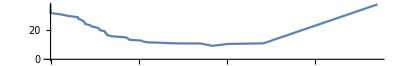

```mathematica
ListPlot[pt["A"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["WA"]

```mathematica
meth="WA"
```

WA

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,11.0542,9.86071,9.2032,9.97093,10.7684,11.084,11.793,12.3025,12.853,13.6699,14.3033,15.1956,16.0411,16.8715,17.7336,18.4634,19.3361,20.213,21.0772,21.824,22.6946,23.5863,24.503,25.4294,26.3276,27.2468,28.1823,29.1247,30.0674,31.0316,32.,33.,34.,35.,36.,37.,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{5.64929,3.6417,2.83627,2.34774,2.03674,1.90489,1.73514,1.65253,1.60666,1.58344,1.54483,1.08802,1.00798,0.994135,0.961533,0.952993,0.927675,0.92273,0.844398,0.820546,0.819333,0.669325,0.659033,0.588454,0.581246,0.5617,0.522399,0.468095,0.466146,0.292172,0.183172,0.,0.,0.,0.,0.,0.,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,37,37,37,37,37,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{5.64929,38.},{3.6417,11.0542},{2.83627,9.86071},{2.34774,9.2032},{2.03674,9.97093},{1.90489,10.7684},{1.73514,11.084},{1.65253,11.793},{1.60666,12.3025},{1.58344,12.853},{1.54483,13.6699},{1.08802,14.3033},{1.00798,15.1956},{0.994135,16.0411},{0.961533,16.8715},{0.952993,17.7336},{0.927675,18.4634},{0.92273,19.3361},{0.844398,20.213},{0.820546,21.0772},{0.819333,21.824},{0.669325,22.6946},{0.659033,23.5863},{0.588454,24.503},{0.581246,25.4294},{0.5617,26.3276},{0.522399,27.2468},{0.468095,28.1823},{0.466146,29.1247},{0.292172,30.0674},{0.183172,31.0316},{0.,32.},{0.,33.},{0.,34.},{0.,35.},{0.,36.},{0.,37.},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.525937

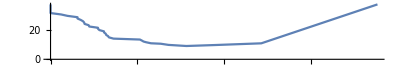

```mathematica
ListPlot[pt["WA"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["W"]

```mathematica
meth="W"
```

W

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,13.9898,11.7349,11.6723,10.1189,10.7373,11.081,11.6546,12.45,13.0071,13.7114,14.3431,15.079,15.736,16.5681,17.4528,18.3099,19.1843,20.0516,20.9267,21.7938,22.6764,23.573,24.4897,25.4008,26.3196,27.2468,28.1823,29.1247,30.0674,31.0316,32.,33.,34.,35.,36.,37.,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{36.6737,10.7161,7.67005,6.97161,6.28158,5.51745,3.68258,3.62661,3.19682,2.3346,2.31466,2.23878,2.20387,1.43447,1.43198,1.05103,1.02298,1.00798,0.961533,0.951732,0.92273,0.774995,0.723301,0.71254,0.592902,0.588454,0.522399,0.468095,0.466146,0.292172,0.244229,0.,0.,0.,0.,0.,0.,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,37,37,37,37,37,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{36.6737,38.},{10.7161,13.9898},{7.67005,11.7349},{6.97161,11.6723},{6.28158,10.1189},{5.51745,10.7373},{3.68258,11.081},{3.62661,11.6546},{3.19682,12.45},{2.3346,13.0071},{2.31466,13.7114},{2.23878,14.3431},{2.20387,15.079},{1.43447,15.736},{1.43198,16.5681},{1.05103,17.4528},{1.02298,18.3099},{1.00798,19.1843},{0.961533,20.0516},{0.951732,20.9267},{0.92273,21.7938},{0.774995,22.6764},{0.723301,23.573},{0.71254,24.4897},{0.592902,25.4008},{0.588454,26.3196},{0.522399,27.2468},{0.468095,28.1823},{0.466146,29.1247},{0.292172,30.0674},{0.244229,31.0316},{0.,32.},{0.,33.},{0.,34.},{0.,35.},{0.,36.},{0.,37.},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.420785

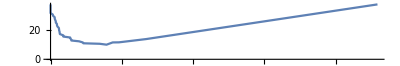

```mathematica
ListPlot[pt["W"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["C"]

```mathematica
meth="C"
```

C

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,11.0542,9.78607,9.41177,9.56526,10.1248,10.8039,11.5555,12.3406,12.9108,13.523,14.3348,15.1804,15.967,16.6666,17.5368,18.3031,19.2151,20.091,20.9563,21.8101,22.6946,23.5863,24.5124,25.4101,26.3451,27.2629,28.2053,29.1249,30.0674,31.0316,32.,33.,34.,35.,36.,37.,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{4.30864,1.92345,1.73955,1.71673,1.48359,1.24598,1.23731,1.2313,1.19898,1.15733,1.02204,0.961533,0.954164,0.936237,0.92273,0.746259,0.729913,0.713799,0.681986,0.646992,0.645681,0.596282,0.588454,0.581246,0.522399,0.482201,0.468095,0.466146,0.444676,0.292172,0.183172,0.,0.,0.,0.,0.,0.,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,37,37,37,37,37,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{4.30864,38.},{1.92345,11.0542},{1.73955,9.78607},{1.71673,9.41177},{1.48359,9.56526},{1.24598,10.1248},{1.23731,10.8039},{1.2313,11.5555},{1.19898,12.3406},{1.15733,12.9108},{1.02204,13.523},{0.961533,14.3348},{0.954164,15.1804},{0.936237,15.967},{0.92273,16.6666},{0.746259,17.5368},{0.729913,18.3031},{0.713799,19.2151},{0.681986,20.091},{0.646992,20.9563},{0.645681,21.8101},{0.596282,22.6946},{0.588454,23.5863},{0.581246,24.5124},{0.522399,25.4101},{0.482201,26.3451},{0.468095,27.2629},{0.466146,28.2053},{0.444676,29.1249},{0.292172,30.0674},{0.183172,31.0316},{0.,32.},{0.,33.},{0.,34.},{0.,35.},{0.,36.},{0.,37.},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.442978

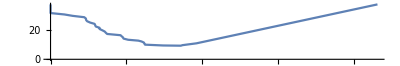

```mathematica
ListPlot[pt["C"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

### Plot

```mathematica
dAreaRatio[pt["A"]]
dAreaRatio[pt["WA"]]
dAreaRatio[pt["W"]]
dAreaRatio[pt["C"]]
```

0.519664

0.525937

0.420785

0.442978

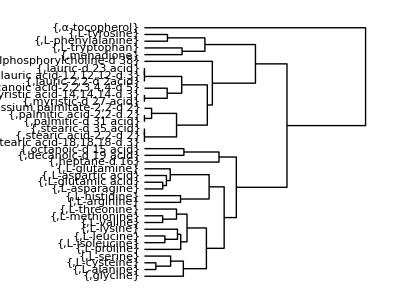

```mathematica
DendrogramPlot[lpaaag["WA"],LeafLabels->({LPAAFig45[[#]],LPAAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

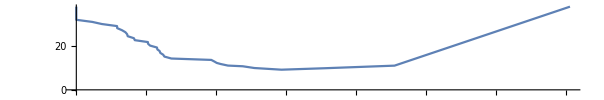

```mathematica
ListPlot[pt["WA"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

## Clustering of Amino Acids + Lipids (2)

### Data

Getting the information of lipids

Merging and Clustering

Distance Matrix

```mathematica
(repElmLPAAAdjMat=Map[repConnection[#,2#&,0]&,elmLPAAAdjMat,{1}])//Short
```

{{{6,2,2,0,0,0,0,0,2,2},{2,6,0,2,4,0,0,0,0,0},«6»,{2,0,0,0,0,0,0,0,1,0},{2,0,0,0,0,0,0,0,0,1}},«36»,{«1»}}

```mathematica
(repLPAADmat=Outer[eigenSpectrumDistance,repElmLPAAAdjMat,elmLPAAAdjMat,1])//Dimensions
```

{38,38}

### Clustering

```mathematica
lpaaag["A"]=DirectAgglomerate[repLPAADmat,Linkage->"Average"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,3.89436,2,1],2,4.08396,3,1],6,4.15304,4,1],12,4.34877,5,1],Cluster[7,10,3.71722,1,1],4.48052,6,2],8,4.75874,8,1],Cluster[5,14,4.92509,1,1],5.00227,9,2],Cluster[Cluster[4,16,4.32732,1,1],13,4.97064,2,1],5.14284,11,3],Cluster[9,19,5.00492,1,1],5.24319,14,2],Cluster[15,18,4.59368,1,1],5.45755,16,2],23,5.60145,18,1],17,6.06152,19,1],20,6.6536,20,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[35,38,7.58233,1,1],36,7.84804,2,1],Cluster[Cluster[Cluster[Cluster[25,31,6.88481,1,1],Cluster[Cluster[26,Cluster[Cluster[29,Cluster[22,Cluster[24,21,4.62,1,1],5.25986,1,2],5.62261,1,3],27,6.20158,4,1],6.6522,1,5],28,6.84029,6,1],7.01368,2,7],30,7.19591,9,1],33,7.30753,10,1],7.88622,3,11],34,7.98177,14,1],37,8.2816,15,1],32,8.6344,16,1],9.11363,21,17]

```mathematica
lpaaag["WA"]=DirectAgglomerate[repLPAADmat,Linkage->"WeightedAverage"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,3.89436,2,1],2,4.06901,3,1],6,4.10547,4,1],Cluster[7,10,3.71722,1,1],4.32247,5,2],12,4.36208,7,1],14,4.54247,8,1],8,4.75684,9,1],5,4.78994,10,1],Cluster[4,16,4.32732,1,1],4.83382,11,2],9,4.93351,13,1],13,5.11052,14,1],Cluster[15,18,4.59368,1,1],5.19114,15,2],19,5.28783,17,1],23,5.56635,18,1],17,5.61809,19,1],20,5.92507,20,1],Cluster[Cluster[26,Cluster[27,Cluster[Cluster[29,Cluster[Cluster[24,21,4.62,1,1],22,5.25986,2,1],5.5712,1,3],25,5.90316,4,1],6.14309,1,5],6.30305,1,6],28,6.4827,7,1],6.53326,21,8],30,6.65823,29,1],31,6.82181,30,1],34,6.86311,31,1],35,6.91736,32,1],36,7.07628,33,1],32,7.17141,34,1],33,7.21011,35,1],37,7.30756,36,1],38,7.68311,37,1]

```mathematica
lpaaag["W"]=DirectAgglomerate[repLPAADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,3.98463,2,1],Cluster[Cluster[2,6,4.11048,1,1],12,4.28188,2,1],4.56724,3,3],5,4.91669,6,1],8,5.13273,7,1],Cluster[Cluster[7,10,3.71722,1,1],14,4.73625,2,1],5.39631,8,3],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[4,16,4.32732,1,1],13,5.18508,2,1],23,5.71194,3,1],Cluster[9,19,5.00492,1,1],5.89862,4,2],17,6.01637,6,1],Cluster[Cluster[15,18,4.59368,1,1],20,6.07126,2,1],7.07606,7,3],7.22711,11,10],Cluster[Cluster[Cluster[33,Cluster[Cluster[Cluster[31,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[29,Cluster[Cluster[21,24,4.62,1,1],22,5.47315,2,1],5.83352,1,3],27,6.25973,4,1],25,6.54076,5,1],26,6.70135,6,1],28,6.91617,7,1],30,7.128,8,1],34,7.20198,9,1],7.36563,1,10],36,7.5353,11,1],32,7.81978,12,1],7.92065,1,13],37,8.26097,14,1],Cluster[38,35,7.58233,1,1],8.44115,15,2],20.6334,21,17]

```mathematica
lpaaag["C"]=DirectAgglomerate[repLPAADmat,Linkage->"Centroid"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,2.98847,2,1],7,2.75447,3,1],2,2.68928,4,1],10,2.56849,5,1],6,2.64179,6,1],12,2.58691,7,1],14,2.70626,8,1],4,2.8388,9,1],8,2.81521,10,1],16,2.79748,11,1],5,2.76501,12,1],9,2.8315,13,1],18,2.84817,14,1],13,2.94109,15,1],19,3.10062,16,1],15,3.0552,17,1],23,3.27887,18,1],17,3.28751,19,1],22,3.51006,20,1],20,3.75155,21,1],29,3.90174,22,1],24,3.84243,23,1],26,3.90395,24,1],25,3.88199,25,1],27,3.86231,26,1],21,3.92405,27,1],28,3.87476,28,1],30,3.8835,29,1],31,4.01444,30,1],34,4.02097,31,1],35,4.04231,32,1],36,4.16958,33,1],32,4.23116,34,1],33,4.23643,35,1],37,4.30208,36,1],38,4.64573,37,1]

### Selection

#### Method["A"]

```mathematica
meth="A"
```

A

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,17.6658,12.7142,11.6504,11.776,12.5577,12.7561,12.707,13.3315,14.2141,15.2325,15.904,16.7351,17.4355,18.3678,19.224,20.0238,20.6246,21.3049,22.5412,23.3582,24.4583,25.6375,26.2091,27.3161,28.1202,28.8856,29.7481,30.4738,31.1787,32.2945,33.0996,33.8307,34.7608,35.6589,36.3577,37.1257,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{9.11363,8.6344,8.2816,7.98177,7.88622,7.84804,7.58233,7.30753,7.19591,7.01368,6.88481,6.84029,6.6536,6.6522,6.20158,6.06152,5.62261,5.60145,5.45755,5.25986,5.24319,5.14284,5.00492,5.00227,4.97064,4.92509,4.75874,4.62,4.59368,4.48052,4.34877,4.32732,4.15304,4.08396,3.89436,3.71722,3.62353,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{9.11363,38.},{8.6344,17.6658},{8.2816,12.7142},{7.98177,11.6504},{7.88622,11.776},{7.84804,12.5577},{7.58233,12.7561},{7.30753,12.707},{7.19591,13.3315},{7.01368,14.2141},{6.88481,15.2325},{6.84029,15.904},{6.6536,16.7351},{6.6522,17.4355},{6.20158,18.3678},{6.06152,19.224},{5.62261,20.0238},{5.60145,20.6246},{5.45755,21.3049},{5.25986,22.5412},{5.24319,23.3582},{5.14284,24.4583},{5.00492,25.6375},{5.00227,26.2091},{4.97064,27.3161},{4.92509,28.1202},{4.75874,28.8856},{4.62,29.7481},{4.59368,30.4738},{4.48052,31.1787},{4.34877,32.2945},{4.32732,33.0996},{4.15304,33.8307},{4.08396,34.7608},{3.89436,35.6589},{3.71722,36.3577},{3.62353,37.1257},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.271676

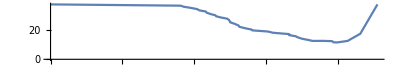

```mathematica
ListPlot[pt["A"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["WA"]

```mathematica
meth="WA"
```

WA

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,11.0542,9.23161,9.14473,9.54446,10.1358,10.8777,11.6611,12.4644,13.3314,14.9443,15.7795,16.7351,17.6571,18.3678,19.224,20.0238,20.6246,21.3049,22.0453,22.8686,24.0728,25.0187,25.9672,27.0135,27.9605,28.8347,29.5589,30.2623,31.1787,32.0369,32.7683,33.8307,34.7608,35.6589,36.3577,37.1257,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{7.68311,7.30756,7.21011,7.17141,7.07628,6.91736,6.86311,6.82181,6.65823,6.53326,6.4827,6.30305,6.14309,5.92507,5.90316,5.61809,5.5712,5.56635,5.28783,5.25986,5.19114,5.11052,4.93351,4.83382,4.78994,4.75684,4.62,4.59368,4.54247,4.36208,4.32732,4.32247,4.10547,4.06901,3.89436,3.71722,3.62353,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{7.68311,38.},{7.30756,11.0542},{7.21011,9.23161},{7.17141,9.14473},{7.07628,9.54446},{6.91736,10.1358},{6.86311,10.8777},{6.82181,11.6611},{6.65823,12.4644},{6.53326,13.3314},{6.4827,14.9443},{6.30305,15.7795},{6.14309,16.7351},{5.92507,17.6571},{5.90316,18.3678},{5.61809,19.224},{5.5712,20.0238},{5.56635,20.6246},{5.28783,21.3049},{5.25986,22.0453},{5.19114,22.8686},{5.11052,24.0728},{4.93351,25.0187},{4.83382,25.9672},{4.78994,27.0135},{4.75684,27.9605},{4.62,28.8347},{4.59368,29.5589},{4.54247,30.2623},{4.36208,31.1787},{4.32732,32.0369},{4.32247,32.7683},{4.10547,33.8307},{4.06901,34.7608},{3.89436,35.6589},{3.71722,36.3577},{3.62353,37.1257},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.229899

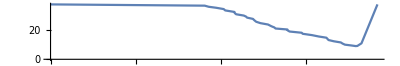

```mathematica
ListPlot[pt["WA"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["W"]

```mathematica
meth="W"
```

W

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,17.6658,13.3653,12.0365,11.9147,12.1784,11.958,12.5675,13.3315,15.0414,15.7695,16.6317,18.1944,19.0132,19.9566,20.866,21.6971,21.933,22.7775,23.838,24.4311,24.821,25.6375,26.8858,27.6827,28.5591,29.1376,30.0345,30.8652,31.5903,32.2945,33.3267,34.0557,34.7684,35.6589,36.3577,37.1257,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{20.6334,8.44115,8.26097,7.92065,7.81978,7.58233,7.5353,7.36563,7.22711,7.20198,7.128,7.07606,6.91617,6.70135,6.54076,6.25973,6.07126,6.01637,5.89862,5.83352,5.71194,5.47315,5.39631,5.18508,5.13273,5.00492,4.91669,4.73625,4.62,4.59368,4.56724,4.32732,4.28188,4.11048,3.98463,3.71722,3.62353,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{20.6334,38.},{8.44115,17.6658},{8.26097,13.3653},{7.92065,12.0365},{7.81978,11.9147},{7.58233,12.1784},{7.5353,11.958},{7.36563,12.5675},{7.22711,13.3315},{7.20198,15.0414},{7.128,15.7695},{7.07606,16.6317},{6.91617,18.1944},{6.70135,19.0132},{6.54076,19.9566},{6.25973,20.866},{6.07126,21.6971},{6.01637,21.933},{5.89862,22.7775},{5.83352,23.838},{5.71194,24.4311},{5.47315,24.821},{5.39631,25.6375},{5.18508,26.8858},{5.13273,27.6827},{5.00492,28.5591},{4.91669,29.1376},{4.73625,30.0345},{4.62,30.8652},{4.59368,31.5903},{4.56724,32.2945},{4.32732,33.3267},{4.28188,34.0557},{4.11048,34.7684},{3.98463,35.6589},{3.71722,36.3577},{3.62353,37.1257},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.259912

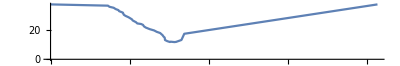

```mathematica
ListPlot[pt["W"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["C"]

```mathematica
meth="C"
```

C

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,11.0542,9.23161,9.14473,9.54446,10.1358,10.8777,11.6611,12.4644,13.3314,14.1994,15.0875,16.0084,16.9219,17.8245,18.759,19.6085,20.3667,21.3199,22.1418,22.8359,23.8238,24.5719,25.5302,26.4352,27.387,28.3536,29.1656,30.0717,30.9909,31.9085,32.7683,33.7284,34.5624,35.5145,36.4248,37.1257,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{4.64573,4.30208,4.23643,4.23116,4.16958,4.04231,4.02097,4.01444,3.92405,3.90395,3.90174,3.8835,3.88199,3.87476,3.86231,3.84243,3.75155,3.62353,3.51006,3.28751,3.27887,3.10062,3.0552,2.98847,2.94109,2.84817,2.8388,2.8315,2.81521,2.79748,2.76501,2.75447,2.70626,2.68928,2.64179,2.58691,2.56849,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{4.64573,38.},{4.30208,11.0542},{4.23643,9.23161},{4.23116,9.14473},{4.16958,9.54446},{4.04231,10.1358},{4.02097,10.8777},{4.01444,11.6611},{3.92405,12.4644},{3.90395,13.3314},{3.90174,14.1994},{3.8835,15.0875},{3.88199,16.0084},{3.87476,16.9219},{3.86231,17.8245},{3.84243,18.759},{3.75155,19.6085},{3.62353,20.3667},{3.51006,21.3199},{3.28751,22.1418},{3.27887,22.8359},{3.10062,23.8238},{3.0552,24.5719},{2.98847,25.5302},{2.94109,26.4352},{2.84817,27.387},{2.8388,28.3536},{2.8315,29.1656},{2.81521,30.0717},{2.79748,30.9909},{2.76501,31.9085},{2.75447,32.7683},{2.70626,33.7284},{2.68928,34.5624},{2.64179,35.5145},{2.58691,36.4248},{2.56849,37.1257},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.201906

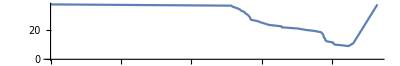

```mathematica
ListPlot[pt["C"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

### Plot

```mathematica
dAreaRatio[pt["A"]]
dAreaRatio[pt["WA"]]
dAreaRatio[pt["W"]]
dAreaRatio[pt["C"]]
```

0.271676

0.229899

0.259912

0.201906

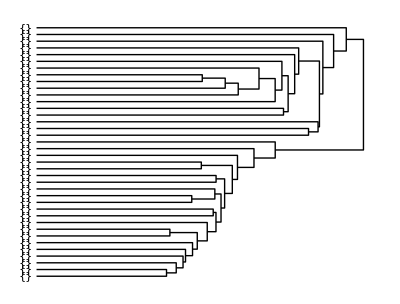

```mathematica
dp3=DendrogramPlot[lpaaag["A"],LeafLabels->({LPAAFig45[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

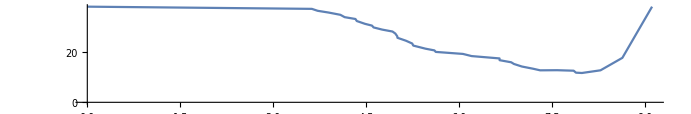

```mathematica
lp3=ListPlot[pt["A"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

## Chart

### Object

```mathematica
box[{x1_,y1_},{x2_,y2_}]:=Line[{{x1,y1},{x1,y2},{x2,y2},{x2,y1},{x1,y1}}]
```

SI plot

```mathematica
b1=box[{0,0},{9.12,38}]
```

Line[{{0,0},{0,38},{9.12,38},{9.12,0},{0,0}}]

```mathematica
t1=Text[Style["A",Large],{2,20}]
t2=Text[Style["B",Large],{7.4,20}]
t3=Text["SI",{-0.5,18}]
t4=Text["Distance",{8.75,-7}]
```

Text[A,{2,20}]

Text[B,{7.4,20}]

Text[SI,{-0.5,18}]

Text[Distance,{8.75,-7}]

```mathematica
cd={DisplayFunction->Identity,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},AxesOrigin->{0,0},PlotRange->{{-0.5,9.113626486361031},{-8,38.}},PlotRangeClipping->True,ImagePadding->All,DisplayFunction->Identity,AspectRatio->1/6,Axes->{True,True},AxesLabel->{None,None},AxesOrigin->{0,0},DisplayFunction:>Identity,Frame->{{False,False},{False,False}},FrameLabel->{{None,None},{None,None}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},GridLines->{None,None},GridLinesStyle->Directive[GrayLevel[0.5, 0.4]],Method->{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotRange->{{0,9.113626486361031},{0,38.}},PlotRangeClipping->True,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks->{Automatic,Automatic}};
```

```mathematica
Graphics[{RGBColor[{0.5,0.6,0.7}],b1,t1,t2,lp3[[1]],RGBColor[{0,0,0}],t3,t4},cd]
```

-Graphics-

Bond Matrix

```mathematica
{{"a",B,B,X1},
{B,"b",B,X2},
{B,B,"c",X3},
{X1,X2,X3,"d"}}//MatrixForm
{{"e",X4,B},
{X4,"f",X5},
{B,X5,"g"}}//MatrixForm
```

(a | B | B | X1
B | b | B | X2
B | B | c | X3
X1 | X2 | X3 | d)

(e | X4 | B
X4 | f | X5
B | X5 | g)

Flow :

```mathematica
coA={-1,0};coB={1,0}
```

{1,0}

:Row1

```mathematica
bA=box[coA+{0,-0.75}+{0.8,0.2},coA+{0,-0.75}+{-0.8,-0.2}]
```

Line[{{-0.2,-0.55},{-0.2,-0.95},{-1.8,-0.95},{-1.8,-0.55},{-0.2,-0.55}}]

```mathematica
bB=box[coB+{0,-0.75}+{0.8,0.2},coB+{0,-0.75}+{-0.8,-0.2}]
```

Line[{{1.8,-0.55},{1.8,-0.95},{0.2,-0.95},{0.2,-0.55},{1.8,-0.55}}]

```mathematica
tA=Text["Compound A",coA+{0,-0.75}]
```

Text[Compound A,{-1,-0.75}]

```mathematica
tB=Text["Compound B",coB+{0,-0.75}]
```

Text[Compound B,{1,-0.75}]

:Row2(not used)

```mathematica
bA2=box[coA+{0.8,0.2}+{0,-0.75},coA+{-0.8,-0.2}+{0,-0.75}]
```

Line[{{-0.2,-0.55},{-0.2,-0.95},{-1.8,-0.95},{-1.8,-0.55},{-0.2,-0.55}}]

```mathematica
bB2=box[coB+{0.8,0.2}+{0,-0.75},coB+{-0.8,-0.2}+{0,-0.75}]
```

Line[{{1.8,-0.55},{1.8,-0.95},{0.2,-0.95},{0.2,-0.55},{1.8,-0.55}}]

```mathematica
tA2=Text["CA[A] = CountAtoms(A)",coA+{0,-0.75}]
```

Text[CA[A] = CountAtoms(A),{-1,-0.75}]

```mathematica
tB2=Text["CA[B] = CountAtoms(B)",coB+{0,-0.75}]
```

Text[CA[B] = CountAtoms(B),{1,-0.75}]

:Row3

```mathematica
bmc=box[{0,-1.25}+{0.75,0.15},{0,-1.25}+{-0.75,-0.15}]
```

Line[{{0.75,-1.1},{0.75,-1.4},{-0.75,-1.4},{-0.75,-1.1},{0.75,-1.1}}]

```mathematica
mc=Text["AC = AtomCount(A,B)",{0,-1.25}]
```

Text[AC = AtomCount(A,B),{0,-1.25}]

:Row4

```mathematica
bA3=box[coA+{0.8,0.2}+{0,-1.75},coA+{-0.8,-0.2}+{0,-1.75}]
```

Line[{{-0.2,-1.55},{-0.2,-1.95},{-1.8,-1.95},{-1.8,-1.55},{-0.2,-1.55}}]

```mathematica
bB3=box[coB+{0.8,0.2}+{0,-1.75},coB+{-0.8,-0.2}+{0,-1.75}]
```

Line[{{1.8,-1.55},{1.8,-1.95},{0.2,-1.95},{0.2,-1.55},{1.8,-1.55}}]

```mathematica
tA3=Text["BM[A] = AddBond(A,AC)",coA+{0,-1.75}]
```

Text[BM[A] = AddBond(A,AC),{-1,-1.75}]

```mathematica
tB3=Text["BM[B] = AddBond(B,AC)",coB+{0,-1.75}]
```

Text[BM[B] = AddBond(B,AC),{1,-1.75}]

:Row5

```mathematica
bA4=box[coA+{0.8,0.2}+{0,-2.4},coA+{-0.8,-0.2}+{0,-2.4}]
```

Line[{{-0.2,-2.2},{-0.2,-2.6},{-1.8,-2.6},{-1.8,-2.2},{-0.2,-2.2}}]

```mathematica
bB4=box[coB+{0.8,0.2}+{0,-2.4},coB+{-0.8,-0.2}+{0,-2.4}]
```

Line[{{1.8,-2.2},{1.8,-2.6},{0.2,-2.6},{0.2,-2.2},{1.8,-2.2}}]

```mathematica
tA4=Text["EVL[A] = Nor(Eigvl(BM[A]))",coA+{0,-2.4}]
```

Text[EVL[A] = Nor(Eigvl(BM[A])),{-1,-2.4}]

```mathematica
tB4=Text["EVL[B] = Nor(Eigvl(BM[B]))",coB+{0,-2.4}]
```

Text[EVL[B] = Nor(Eigvl(BM[B])),{1,-2.4}]

:Row6

```mathematica
bidx=box[{0,-3}+{0.95,0.15},{0,-3}+{-0.95,-0.5}]
```

Line[{{0.95,-2.85},{0.95,-3.5},{-0.95,-3.5},{-0.95,-2.85},{0.95,-2.85}}]

```mathematica
tidx=Text["IDX[A,B] = Inner(EVL[A],EVL[B])
OR
IDX[A,B] = Dist(EVL[A],EVL[B])",{0,-3.2}]
```

Text[IDX[A,B] = Inner(EVL[A],EVL[B])
OR
IDX[A,B] = Dist(EVL[A],EVL[B]),{0,-3.2}]

:Arrow

```mathematica
ar={Arrow[{coA+{0,-0.95},coA+{0,-1.55}}],Arrow[{coB+{0,-0.95},coB+{0,-1.55}}],
Arrow[{coA+{0,-0.95},coA+{0.9,-1.1}}],Arrow[{coB+{0,-0.95},coB+{-0.9,-1.1}}],
Arrow[{coA+{0.9,-1.4},coA+{0,-1.55}}],Arrow[{coB+{-0.9,-1.4},coB+{0,-1.55}}],
Arrow[{coA+{0,-1.95},coA+{0,-2.2}}],Arrow[{coB+{0,-1.95},coB+{0,-2.2}}],
Arrow[{coA+{0,-2.6},coA+{0.9,-2.85}}],Arrow[{coB+{0,-2.6},coB+{-0.9,-2.85}}]
}
```

{Arrow[{{-1,-0.95},{-1,-1.55}}],Arrow[{{1,-0.95},{1,-1.55}}],Arrow[{{-1,-0.95},{-0.1,-1.1}}],Arrow[{{1,-0.95},{0.1,-1.1}}],Arrow[{{-0.1,-1.4},{-1,-1.55}}],Arrow[{{0.1,-1.4},{1,-1.55}}],Arrow[{{-1,-1.95},{-1,-2.2}}],Arrow[{{1,-1.95},{1,-2.2}}],Arrow[{{-1,-2.6},{-0.1,-2.85}}],Arrow[{{1,-2.6},{0.1,-2.85}}]}

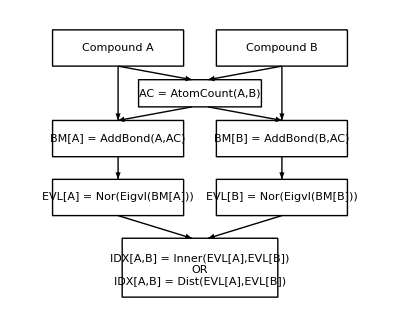

```mathematica
Graphics[{tA,bA,tB,bB(*,tA2,bA2,tB2,bB2*),mc,bmc,bA3,bB3,tA3,tB3,bA4,bB4,tA4,tB4,bidx,tidx,ar}]
```

Table

```mathematica
TableForm[{{"Classify[A,α]","Classify[B,α]",""},
{"Classify[A,β]","",""},
{"","",""},
{"     ↓","",""},
{"","",""},
{"指標による選択","",""}
},
TableHeadings->{{"Parameter α","Parameter β","..."},{"隣接行列 A","隣接行列 B","..."}}]
```

| 隣接行列 A | 隣接行列 B | ...
Parameter α | Classify[A,α] | Classify[B,α] | 
Parameter β | Classify[A,β] |  | 
... |  |  | 
 |      ↓ |  | 
 |  |  | 
 | 指標による選択 |  |

## References

Characteristics of eigen system
CharacteristicsOfEigen.nb

The 27th Annual Conference of the Japanese Society for Artificial Intelligence, 203, 2 C1 - 1
Structure_Characteristics _Profiling.nb

Cospectral Graphs by Eric W. W.
CospectralGraphs.nb

Cluster Validity Index
SI.nb